### Determinant and Volume

```mathematica
Ds3D=({{x1-x4, x2-x4, x3-x4}, {y1-y4, y2-y4, y3-y4}, {z1-z4, z2-z4, z3-z4}})/.{z4->-z1-z2-z3,y4->-y1-y2-y3,x4->-x1-x2-x3}
Ds2D=({{x1-x3, x2-x3}, {y1-y3, y2-y3}});
a=√((x3-x1)^2+(y3-y1)^2);
b=√((x3-x2)^2+(y3-y2)^2);
c=√((x1-x2)^2+(y1-y2)^2);
s=(a+b+c)/2;
Vh=√(s(s-a)(s-b)(s-c));
FullSimplify[{Vh,Det[Ds2D]},Reals];
```

{{2 x1+x2+x3,x1+2 x2+x3,x1+x2+2 x3},{2 y1+y2+y3,y1+2 y2+y3,y1+y2+2 y3},{2 z1+z2+z3,z1+2 z2+z3,z1+z2+2 z3}}

```mathematica
λ[k_,ν_]=(k ν)/((1+ν)(1-2ν));
μ[k_,ν_]=k/(2(1+ν));
LameCoefficients[κ_,ν_]={λ[k,ν], μ[k,ν]};
```

```mathematica
N@Solve[λ[1, ν]==1,ν]
λ[1.0,0.33]
μ[1.0,0.33]
```

{{ν→-1.36603},{ν→0.366025}}

0.729766

0.37594

```mathematica
$Assumptions=_∈Reals;
Id= IdentityMatrix[2];
VenantKirchhoffPotential[F_,k_,ν_]:=Module[{E},
E=1/2(Fᵀ.F-Id);
μ[k,ν]Tr[E.E]+λ[k,ν]/2 Tr[E]^2
]
VenantKirchhoffStress[F_,k_,ν_]:=Module[{E},
E=1/2(Fᵀ.F-Id);
F.(2 μ[k,ν] E+λ[k,ν] Tr[E] Id)
]
VenantKirchhoffStressDifferential[F_,dF_,k_,ν_]:=Module[{E,dE},
E=1/2(Fᵀ.F-Id);dE=1/2(dFᵀ.F+Fᵀ.dF);
dF.(2 μ[k,ν] E+λ[k,ν] Tr[E] Id)+F.(2 μ[k,ν] dE+λ[k,ν] Tr[dE] Id)
]
Ds[tr_]:=Transpose[tr[[1;;2]]-{tr[[3]],tr[[3]]}];
Bm[tr_]:=Inverse[Ds[tr]]

ElasticForce[P_,vA_]:=Module[{H},
H=-Abs[Det[Ds[vA]]]/2P.(Inverse[Ds[vA]])ᵀ;
{Hᵀ[[1]],Hᵀ[[2]],-Hᵀ[[1]]-Hᵀ[[2]]}
]
F[vA_,vB_]:=Ds[vB].Bm[vA];
```

```mathematica
v={{0,0},{0,1},{1,0}}
Ds[v]//MatrixForm
Bm[v]//MatrixForm
```

{{0,0},{0,1},{1,0}}

(-1 | -1
0 | 1)

(-1 | -1
0 | 1)

```mathematica
vA={{0,0},{0,1},{1,0}};
vB={{0,-1},{2,2},{1,-1}};
vB=vInit;
dv={{1,0},{0,1},{1,1}};
s=VenantKirchhoffStress[F[vA,vB],1,0.33]
ds=VenantKirchhoffStressDifferential[F[vA,vB],F[vA,dv],1,0.33]
ψ=VenantKirchhoffPotential[F[vA,vB],1,0.33]
F[vA,vB]
g=ElasticForce[s,vA]
ElasticForce[ds,vA]
ScanLine[α_,v_,vA_]:=Module[{P,f},
f=ElasticForce[VenantKirchhoffStress[F[vA,v],1,0.33],vA];
P=VenantKirchhoffStress[F[vA,v+α f],1,0.33];
{-Flatten[ElasticForce[P,vA]].Flatten[f]/Norm[Flatten[f]],
VenantKirchhoffPotential[F[vA,v+α f],1,0.33],f}
]
```

{{0.0309598,-0.0789474},{-0.045356,-0.0933437}}

{{-0.739275,-0.0309598},{0.366873,-0.225785}}

0.124776

{{1.,0.},{-0.7,0.3}}

{{-0.0239938,-0.0693498},{0.0394737,0.0466718},{-0.0154799,0.022678}}

{{-0.385117,0.070544},{0.0154799,0.112893},{0.369637,-0.183437}}

0.364883 (1/2 (-1+(1.+0.00851393 α)^2+(-0.7+0.0920279 α)^2)+1/2 (-1+(0.+0.0634675 α)^2+(0.3+0.116022 α)^2))^2+0.37594 (1/4 (-1+(1.+0.00851393 α)^2+(-0.7+0.0920279 α)^2)^2+1/2 ((1.+0.00851393 α) (0.+0.0634675 α)+(-0.7+0.0920279 α) (0.3+0.116022 α))^2+1/4 (-1+(0.+0.0634675 α)^2+(0.3+0.116022 α)^2)^2)

{{0.,0.7},{0.,1.},{1.,0.}}

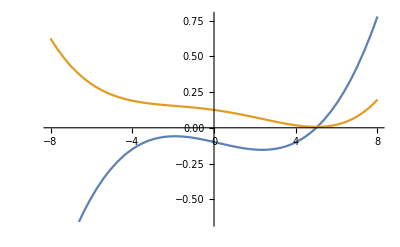

{{1/2 (1.-1.5 α),1/2 (-0.4+0.6 α)},{1/2 (0.+0.5 α),1/2 (-0.3-0.05 α)},{1/2 (0.-0.5 α)+1/2 (-1.+1.5 α),1/2 (0.4-0.6 α)+1/2 (0.3+0.05 α)}}

```mathematica
bla=ScanLine[α,vInit,vA];
bla[[2]]
vInit
Plot[{bla[[1]], bla[[2]]},{α,-8,8}]
```

-1

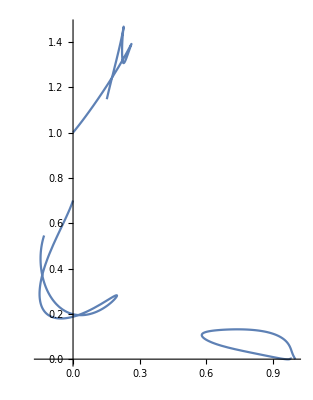

```mathematica
t1=10;
system[t_]=Table[i[j][t],{j,1,3},{i,{xc,yc}}];
Det[Ds[vA]]
rhs=ElasticForce[VenantKirchhoffStress[F[vA,system[t]],1, 0.33],vA];
lhs=system''[t];

y[t_]=system[t];
vInit = vA+0.7{{0,1},{0,0},{0,0}};

sol=NDSolve[{lhs==rhs,
y[0]==vInit,y'[0]==0 vInit},y[t],{t,0,t1},Method->"ExplicitEuler"];
Animate[
Graphics[{PointSize[0.05],Polygon[(system[t]/.sol[[1]])]/.t->u,
Point[(system[t]/.sol)[[1]]/.t->u,VertexColors->{Red, Green, Blue}]}
,Frame->True,PlotRange->{{-2,2},{-2,2}}],{u,0,t1}]
ParametricPlot[system[t]/.sol,{t,0,t1}]
```

```mathematica
x={4,3,9,2,-5}
√(x.x)
N@√Total[x x]
```

{4,3,9,2,-5}

3 √15

11.619